```mathematica
(* Present goal: update the functions to include the effect of strain, and get the new transmission amplitude expression. Then test it to see if it makes physical sense. My current understanding is that phi, phi1, px, and px1, which are only evaluated at the edges of the channϵl, do not change. *)
```

```mathematica
ClearAll["Global`*"]
(*momenta parameters*)
ϕ1[ϕ_,ϵl_,dl_]:=ArcSin[2*(dl)*(1/(ϵl))+Sin[ϕ]];
(*py[ϕ_]:=ϵ*Sin[ϕ]+(d/(lb)^2)*)
px[ϕ_]:=Cos[ϕ];
px1[ϕ_,ϵl_,dl_]:=Cos[ArcSin[2*(dl)*(1/(ϵl))+Sin[ϕ]]];

(*The effect of strain is simply to change the value of dl in u1 and v1
from -d/l to (-d-Subscript[x, o])/l and in u2 and v2 from d/l to (d-Subscript[x, o])/l*)

(*Operators u*)
u1p[ϕ_,ϵl_,dl_]:=ParabolicCylinderD[(((ϵl)^2)/2)-1,Sqrt[2]*((-dl)+ϵl*Sin[ϕ]+dl)] ;
u1m[ϕ_,ϵl_,dl_]:=ParabolicCylinderD[(((ϵl)^2)/2)-1,-1*Sqrt[2]*((-dl)+ϵl*Sin[ϕ]+dl)]
u2p[ϕ_,ϵl_,dl_]:=ParabolicCylinderD[(((ϵl)^2)/2)-1,Sqrt[2]*((dl)+ϵl*Sin[ϕ]+dl)]
u2m[ϕ_,ϵl_,dl_]:=ParabolicCylinderD[(((ϵl)^2)/2)-1,-1*Sqrt[2]*((dl)+ϵl*Sin[ϕ]+dl)]
(*Operators v*)
v1p[ϕ_,ϵl_,dl_]:=ParabolicCylinderD[((ϵl)^2)/2,Sqrt[2]*((-dl)+ϵl*Sin[ϕ]+dl)]
v1m[ϕ_,ϵl_,dl_]:=ParabolicCylinderD[((ϵl)^2)/2,-1*Sqrt[2]*((-dl)+ϵl*Sin[ϕ]+dl)]
v2p[ϕ_,ϵl_,dl_]:=ParabolicCylinderD[((ϵl)^2)/2,Sqrt[2]*((dl)+ϵl*Sin[ϕ]+dl)]
v2m[ϕ_,ϵl_,dl_]:=ParabolicCylinderD[((ϵl)^2)/2,-1*Sqrt[2]*((dl)+ϵl*Sin[ϕ]+dl)]

(*D operator without strain*)
Dop[ϕ_,ϵl_,dl_]:=((ϵl)^2)*Exp[I*(ϕ1[ϕ,ϵl,dl]-ϕ)]*(u1p[ϕ,ϵl,dl]*u2m[ϕ,ϵl,dl]-u2p[ϕ,ϵl,dl]*u1m[ϕ,ϵl,dl])-2*(v1p[ϕ,ϵl,dl]*v2m[ϕ,ϵl,dl]-v2p[ϕ,ϵl,dl]*v1m[ϕ,ϵl,dl])+I*Sqrt[2]*ϵl*(Exp[I*ϕ1[ϕ,ϵl,dl]]*(v1p[ϕ,ϵl,dl]*u2m[ϕ,ϵl,dl]+u2p[ϕ,ϵl,dl]*v1m[ϕ,ϵl,dl])+Exp[-I*ϕ]*(u1p[ϕ,ϵl,dl]*v2m[ϕ,ϵl,dl]+v2p[ϕ,ϵl,dl]*u1m[ϕ,ϵl,dl]))

(*transmission amplitude without strain*)
t[ϕ_,ϵl_,dl_]:=(2*I*ϵl*(u2p[ϕ,ϵl,dl]*v2m[ϕ,ϵl,dl]+v2p[ϕ,ϵl,dl]*u2m[ϕ,ϵl,dl]))/(Exp[I*(px[ϕ]+px1[ϕ,ϵl,dl])*ϵl*dl]*Dop[ϕ,ϵl,dl])


(*transmission equation without strain*)
T[ϕ_,ϵl_,dl_]:=2*px1[ϕ,ϵl,dl]*Cos[ϕ]*t[ϕ,ϵl,dl]*(t[ϕ,ϵl,dl])*


(* Export general graphene transmission expression *)
SetDirectory[NotebookDirectory[]];
Export["Tphi_expr_V0.0.mx",T[ϕ,ϵl,dl]]

"Tphi_expr_V0.0.mx"
```

Tphi_expr_V0.0.mx

Tphi_expr_V0.0.mx

```mathematica
(*D operator with strain*)

Dops[ϕ_,ϵl_,dl_,dl1_,dl2_]:=((ϵl)^2)*Exp[I*(ϕ1[ϕ,ϵl,dl]-ϕ)]*(u1p[ϕ,ϵl,dl1]*u2m[ϕ,ϵl,dl2]-u2p[ϕ,ϵl,dl2]*u1m[ϕ,ϵl,dl1])-2*(v1p[ϕ,ϵl,dl1]*v2m[ϕ,ϵl,dl2]-v2p[ϕ,ϵl,dl2]*v1m[ϕ,ϵl,dl1])+I*Sqrt[2]*ϵl*(Exp[I*ϕ1[ϕ,ϵl,dl]]*(v1p[ϕ,ϵl,dl1]*u2m[ϕ,ϵl,dl2]+u2p[ϕ,ϵl,dl2]*v1m[ϕ,ϵl,dl1])+Exp[-I*ϕ]*(u1p[ϕ,ϵl,dl1]*v2m[ϕ,ϵl,dl2]+v2p[ϕ,ϵl,dl2]*u1m[ϕ,ϵl,dl1]))

(*transmission amplitude with strain*)
ts[ϕ_,ϵl_,dl_,dl1_,dl2_]:=(2*I*ϵl*(u2p[ϕ,ϵl,dl2]*v2m[ϕ,ϵl,dl2]+v2p[ϕ,ϵl,dl2]*u2m[ϕ,ϵl,dl2]))/(Exp[I*(px[ϕ]+px1[ϕ,ϵl,dl])*ϵl*dl]*Dops[ϕ,ϵl,dl,dl1,dl2])

(*transmission equation with strain*)
Ts[ϕ_,ϵl_,dl_,dl1_,dl2_]:=2*px1[ϕ,ϵl,dl]*Cos[ϕ]*ts[ϕ,ϵl,dl,dl1,dl2]*(ts[ϕ,ϵl,dl,dl1,dl2])*
SetDirectory[NotebookDirectory[]];
Export["Tsphi_expr_V0.mx",Ts[ϕ,ϵl,dl,dl1,dl2]];
```

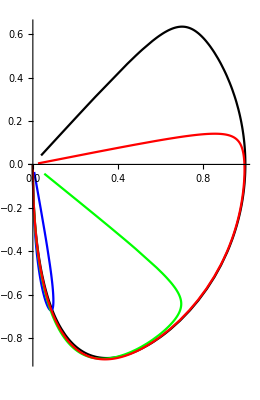

```mathematica
PolarPlot[{T[ϕ,3.7,0.5],T[ϕ,3.7,3.67],T[ϕ,3.7,3],T[ϕ,3.7,1.5]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Black,Blue,Green,Red}]
```

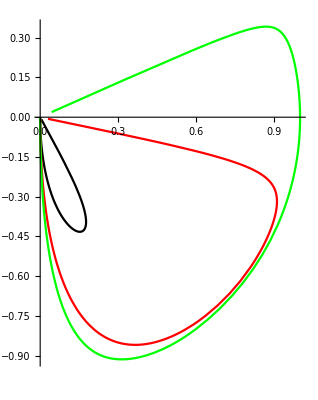

```mathematica
PolarPlot[{T[ϕ,1.6,1.5],T[ϕ,2.5,1.5],T[ϕ,5,1.5]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Black,Red,Green}]
```

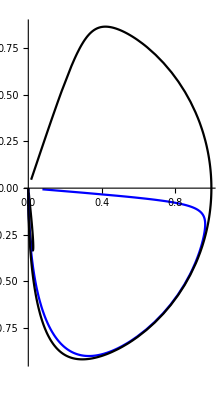

```mathematica
PolarPlot[{T[ϕ,3.7,3.69],T[ϕ,3.7,2.0],T[ϕ,3.7,0.1]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Black,Blue}]
```